tamoaltas - Algo Curioso

-Graphics-

```mathematica
$Assumptions ={n ∈ Integers && n >= 0};
```

A continuación, los coeficientes de f_(2n) que encontré (o que Mathematica encontró) para el problema.

```mathematica
f2n[n_]:=(-1)^(n+1)(((4n+1)Factorial[2n])/(2^(2n+1)(2n-1)(2n+2)Factorial[n]^2))
```

```mathematica
f2nMathematica[n_]:=((1+4 n) √π)/(8 Gamma[3/2-n] Gamma[2+n])
```

```mathematica
fx[x_,l_]:=Sum[f2n[n] LegendreP[2n,x],{n,0,l}]+ 1/2 x
fxMathematica[x_,l_]:=Sum[f2nMathematica[n] LegendreP[2n,x],{n,0,l}]+ 1/2 x
```

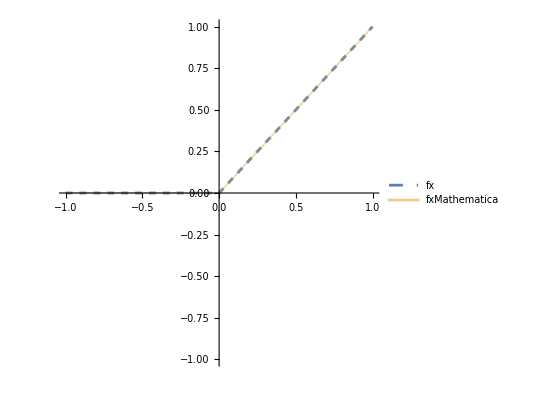

```mathematica
plot = Plot[{fx[x,100],fxMathematica[x,100] },
{x,-1,1},PlotRange->{{-1,1},{-1,1}},
PlotLegends->{"fx", "fxMathematica"},
PlotStyle->{{Dashed, Opacity[1]},{Thick, Opacity[0.5]}},AspectRatio->1
]
```

```mathematica
imagesDir=FileNameJoin[{NotebookDirectory[],"/images" }];
plotName= StringJoin[ {FileBaseName[NotebookFileName[]], ".png"}];
filePath= FileNameJoin[{imagesDir,plotName}];

(* Se crea el directorio si no existe *)
If[!DirectoryQ[imagesDir],CreateDirectory[imagesDir]];

Rasterize[plot,ImageResolution->Automatic,Background->White];
```

```mathematica
Export[filePath,plot,ImageResolution->Automatic];
```